# Correlation func

Functions

```mathematica
importLattice[iIC_,lattIdx_,timepoint_]:=Module[
{latt,lattComplete},
SetDirectory[NotebookDirectory[]];
latt=Import["../../bimol_train_stoch_sim/data/ic_v"<>IntegerString[iIC,10,3]<>"/lattice_v"<>IntegerString[lattIdx,10,3]<>"/lattice/"<>IntegerString[timepoint,10,4]<>".txt","Table"][[;;,1]];

	lattComplete=ConstantArray[0,boxLength];
lattComplete[[latt]]=ConstantArray[1,Length[latt]];

Return[lattComplete];
];
importLattice[iIC_,lattIdx_]:=importLattice[iIC,lattIdx,0];
```

```mathematica
getCount[iIC_,iLatt_,time_]:=Module[
{latt},
latt=importLattice[iIC,iLatt,time];
Return[Total[-2*Abs[latt[[2;;]]-latt[[;;-2]]]+1]/999.0];
];
```

```mathematica
getCountTraj[iIC_,iLatt_,timeStart_,timeEnd_]:=Module[
{corrs},
corrs={};
Do[
AppendTo[corrs,getCount[iIC,iLatt,time]]
,{time,timeStart,timeEnd}];
Return[corrs];
];
```

```mathematica
getMeanCountTraj[iIC_,iLattStart_,iLattEnd_,timeStart_,timeEnd_]:=Module[
{corrs},
corrs={};
Do[
AppendTo[corrs,getCountTraj[iIC,iLatt,timeStart,timeEnd]];
,{iLatt,iLattStart,iLattEnd}];
Return[Mean[corrs]];
];
```

Make figure

```mathematica
icStart=1;
icEnd=50;
```

```mathematica
corrs=Association[];
Monitor[
Do[
corrs[iIC]=getMeanCountTraj[iIC,1,10,0,200];
,{iIC,icStart,icEnd}];
,ProgressIndicator[iIC,{icStart,icEnd}]];
```

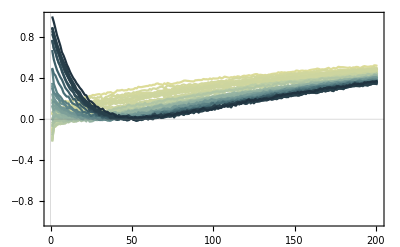

```mathematica
pltCorr=ListLinePlot[Values[corrs][[trajsIdxsSort]],PlotStyle->Reverse[Sort[colsTraj]],PlotRange->{-1,1}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/corr.pdf",pltCorr]
```

../figures/corr.pdf

Legacy

```mathematica
corrs2=Map[corrs[#]&,idxs2];
AppendTo[corrs2,Mean[corrs2]];
cols2=Join[Table[LightGray,{i,1,Length[corrs2]-1}],{Darker[ColorData[97,3]]}]
```

{GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],RGBColor[0.37345400000000006, 0.461046, 0.12992333333333334]}

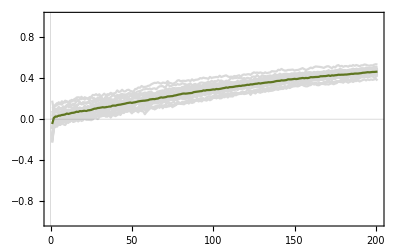

```mathematica
ListLinePlot[corrs2,PlotRange->{-1,1},PlotStyle->cols2]
```

```mathematica
corrs1=Map[corrs[#]&,idxs1];
AppendTo[corrs1,Mean[corrs1]];
cols1=Join[Table[LightGray,{i,1,Length[corrs1]-1}],{ColorData[97,1]}]
```

{GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],RGBColor[0.368417, 0.506779, 0.709798]}

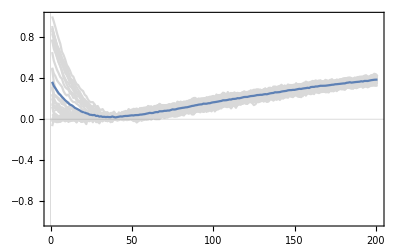

```mathematica
ListLinePlot[corrs1,PlotRange->{-1,1},PlotStyle->cols1]
```